```mathematica
hetsSBS=0.00041;
hetsRNS=0.00064;

densRNS=0.00088;
densSBS=0.00073;
```

```mathematica
bothc[i_]:=Blend[{{0,RGBColor["#ffffff"]},{0.4,RGBColor["#f57a00"]}},i]
```

```mathematica
bothc[i_]:=Blend[{{0,RGBColor["#ffffff"]},{0.4,{RGBColor["#ffffff"],Opacity[0]}}},i]
```

```mathematica
PointLegend[{bothc[0],bothc[0.1],bothc[0.2],bothc[0.3],bothc[0.4]},{0,0.1,0.2,0.3,"0.4 and larger"}]
```

```mathematica
RNShetsA0B0=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/hets_rns_alpha=0.0_beta=0.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsA0B1000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/hets_rns_alpha=0.0_beta=1000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsA0B2000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/hets_rns_alpha=0.0_beta=2000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsA0B3000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/hets_rns_alpha=0.0_beta=3000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsA0B5000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/hets_rns_alpha=0.0_beta=5000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsA0B7000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/hets_rns_alpha=0.0_beta=7000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsA2B0=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/hets_rns_alpha=-2.0_beta=0.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsA2B1000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/hets_rns_alpha=-2.0_beta=1000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsA2B2000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/hets_rns_alpha=-2.0_beta=2000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsA2B3000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/hets_rns_alpha=-2.0_beta=3000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsA2B5000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/hets_rns_alpha=-2.0_beta=5000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsA2B7000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/hets_rns_alpha=-2.0_beta=7000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsA4B0=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/hets_rns_alpha=-4.0_beta=0.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsA4B1000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/hets_rns_alpha=-4.0_beta=1000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsA4B2000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/hets_rns_alpha=-4.0_beta=2000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsA4B3000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/hets_rns_alpha=-4.0_beta=3000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsA4B5000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/hets_rns_alpha=-4.0_beta=5000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsA4B7000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/hets_rns_alpha=-4.0_beta=7000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

Reading Fedya' s code output :

```mathematica
RNShetsFA0B0=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_rns_avg-het_alpha=0.0_beta=0.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsFA0B1000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_rns_avg-het_alpha=0.0_beta=1000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsFA0B2000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_rns_avg-het_alpha=0.0_beta=2000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsFA0B3000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_rns_avg-het_alpha=0.0_beta=3000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsFA0B5000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_rns_avg-het_alpha=0.0_beta=5000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsFA0B7000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_rns_avg-het_alpha=0.0_beta=7000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsFA2B0=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_rns_avg-het_alpha=-2.0_beta=0.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsFA2B1000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_rns_avg-het_alpha=-2.0_beta=1000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsFA2B2000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_rns_avg-het_alpha=-2.0_beta=2000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsFA2B3000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_rns_avg-het_alpha=-2.0_beta=3000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsFA2B5000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_rns_avg-het_alpha=-2.0_beta=5000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsFA2B7000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_rns_avg-het_alpha=-2.0_beta=7000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsFA4B0=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_rns_avg-het_alpha=-4.0_beta=0.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsFA4B1000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_rns_avg-het_alpha=-4.0_beta=1000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsFA4B2000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_rns_avg-het_alpha=-4.0_beta=2000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsFA4B3000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_rns_avg-het_alpha=-4.0_beta=3000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsFA4B5000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_rns_avg-het_alpha=-4.0_beta=5000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsFA4B7000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_rns_avg-het_alpha=-4.0_beta=7000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNSdensFA0B0=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_rns_pols_alpha=0.0_beta=0.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNSdensFA0B1000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_rns_pols_alpha=0.0_beta=1000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNSdensFA0B2000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_rns_pols_alpha=0.0_beta=2000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNSdensFA0B3000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_rns_pols_alpha=0.0_beta=3000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNSdensFA0B5000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_rns_pols_alpha=0.0_beta=5000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNSdensFA0B7000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_rns_pols_alpha=0.0_beta=7000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNSdensFA2B0=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_rns_pols_alpha=-2.0_beta=0.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNSdensFA2B1000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_rns_pols_alpha=-2.0_beta=1000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNSdensFA2B2000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_rns_pols_alpha=-2.0_beta=2000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNSdensFA2B3000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_rns_pols_alpha=-2.0_beta=3000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNSdensFA2B5000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_rns_pols_alpha=-2.0_beta=5000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNSdensFA2B7000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_rns_pols_alpha=-2.0_beta=7000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNSdensFA4B0=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_rns_pols_alpha=-4.0_beta=0.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNSdensFA4B1000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_rns_pols_alpha=-4.0_beta=1000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNSdensFA4B2000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_rns_pols_alpha=-4.0_beta=2000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNSdensFA4B3000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_rns_pols_alpha=-4.0_beta=3000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNSdensFA4B5000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_rns_pols_alpha=-4.0_beta=5000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNSdensFA4B7000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_rns_pols_alpha=-4.0_beta=7000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
SBShetsFA0B0=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_sbs_avg-het_alpha=0.0_beta=0.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
SBShetsFA0B1000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_sbs_avg-het_alpha=0.0_beta=1000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
SBShetsFA0B2000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_sbs_avg-het_alpha=0.0_beta=2000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
SBShetsFA0B3000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_sbs_avg-het_alpha=0.0_beta=3000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
SBShetsFA0B5000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_sbs_avg-het_alpha=0.0_beta=5000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
SBShetsFA0B7000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_sbs_avg-het_alpha=0.0_beta=7000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
SBShetsFA2B0=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_sbs_avg-het_alpha=-2.0_beta=0.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
SBShetsFA2B1000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_sbs_avg-het_alpha=-2.0_beta=1000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
SBShetsFA2B2000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_sbs_avg-het_alpha=-2.0_beta=2000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
SBShetsFA2B3000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_sbs_avg-het_alpha=-2.0_beta=3000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
SBShetsFA2B5000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_sbs_avg-het_alpha=-2.0_beta=5000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
SBShetsFA2B7000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_sbs_avg-het_alpha=-2.0_beta=7000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
SBShetsFA4B0=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_sbs_avg-het_alpha=-4.0_beta=0.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
SBShetsFA4B1000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_sbs_avg-het_alpha=-4.0_beta=1000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
SBShetsFA4B2000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_sbs_avg-het_alpha=-4.0_beta=2000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
SBShetsFA4B3000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_sbs_avg-het_alpha=-4.0_beta=3000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
SBShetsFA4B5000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_sbs_avg-het_alpha=-4.0_beta=5000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
SBShetsFA4B7000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_sbs_avg-het_alpha=-4.0_beta=7000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
SBSdensFA0B0=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_sbs_pols_alpha=0.0_beta=0.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
SBSdensFA0B1000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_sbs_pols_alpha=0.0_beta=1000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
SBSdensFA0B2000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_sbs_pols_alpha=0.0_beta=2000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
SBSdensFA0B3000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_sbs_pols_alpha=0.0_beta=3000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
SBSdensFA0B5000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_sbs_pols_alpha=0.0_beta=5000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
SBSdensFA0B7000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_sbs_pols_alpha=0.0_beta=7000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
SBSdensFA2B0=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_sbs_pols_alpha=-2.0_beta=0.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
SBSdensFA2B1000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_sbs_pols_alpha=-2.0_beta=1000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
SBSdensFA2B2000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_sbs_pols_alpha=-2.0_beta=2000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
SBSdensFA2B3000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_sbs_pols_alpha=-2.0_beta=3000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
SBSdensFA2B5000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_sbs_pols_alpha=-2.0_beta=5000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
SBSdensFA2B7000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_sbs_pols_alpha=-2.0_beta=7000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
SBSdensFA4B0=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_sbs_pols_alpha=-4.0_beta=0.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
SBSdensFA4B1000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_sbs_pols_alpha=-4.0_beta=1000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
SBSdensFA4B2000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_sbs_pols_alpha=-4.0_beta=2000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
SBSdensFA4B3000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_sbs_pols_alpha=-4.0_beta=3000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
SBSdensFA4B5000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_sbs_pols_alpha=-4.0_beta=5000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
SBSdensFA4B7000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/out/rns_points_sbs_pols_alpha=-4.0_beta=7000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
area[μ_,σ_,α_]:=NIntegrate[PDF[SkewNormalDistribution[μ,σ,α],s],{s,0.0005,5*σ}]
```

```mathematica
Table[1.50017325^σ/10000,{σ,0,21,1}]
```

{0.0001,0.000150017,0.000225052,0.000337617,0.000506484,0.000759814,0.00113985,0.00170998,0.00256526,0.00384833,0.00577317,0.00866075,0.0129926,0.0194912,0.0292402,0.0438653,0.0658056,0.0987198,0.148097,0.222171,0.333295,0.5}

```mathematica
Table[-1.50017325^μ/10000,{μ,21,0,-1}]
```

{-0.5,-0.333295,-0.222171,-0.148097,-0.0987198,-0.0658056,-0.0438653,-0.0292402,-0.0194912,-0.0129926,-0.00866075,-0.00577317,-0.00384833,-0.00256526,-0.00170998,-0.00113985,-0.000759814,-0.000506484,-0.000337617,-0.000225052,-0.000150017,-0.0001}

```mathematica
area0=Table[{-1.50017325^μ/10000,1.50017325^σ/10000,0,area[-1.50017325^μ/10000,1.50017325^σ/10000,0]},{μ,21,0,-1},{σ,0,21,1}];
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/overflow_alpha=0_log.txt",area0]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/overflow_alpha=0_log.txt

```mathematica
area2=Table[{-1.50017325^μ/10000,1.50017325^σ/10000,-2,area[-1.50017325^μ/10000,1.50017325^σ/10000,-2]},{μ,21,0,-1},{σ,0,21,1}];
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/overflow_alpha=-2_log.txt",area2]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {0.00384981}. NIntegrate obtained 9.×10^-323 and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {0.000801622062381366989013142809739065342000685632228851318359375}. NIntegrate obtained 1.×10^-323 and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {0.00855689}. NIntegrate obtained 1.5×10^-323 and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/overflow_alpha=-2_log.txt

```mathematica
area4=Table[{-1.50017325^μ/10000,1.50017325^σ/10000,-4,area[-1.50017325^μ/10000,1.50017325^σ/10000,-4]},{μ,21,0,-1},{σ,0,21,1}];
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/overflow_alpha=-4_log.txt",area4]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/overflow_alpha=-4_log.txt

```mathematica
int0=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/overflow_alpha=0_log_processed.txt",{Record,Record,Record,Record},484,RecordSeparators->{","," ","\n"}];
int2=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/overflow_alpha=-2_log_processed.txt",{Record,Record,Record,Record},484,RecordSeparators->{","," ","\n"}];
int4=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/overflow_alpha=-4_log_processed.txt",{Record,Record,Record,Record},484,RecordSeparators->{","," ","\n"}];
```

```mathematica
int0log=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},#[[4]]}&/@int0,InterpolationOrder->1];
```

```mathematica
int2log=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},#[[4]]}&/@int2,InterpolationOrder->1];
```

```mathematica
int4log=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},#[[4]]}&/@int4,InterpolationOrder->1];
```

```mathematica
int0plot=ContourPlot[int0log[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{0.01},ContourShading->{None,{White,Opacity[1]}},Mesh->None,ContourStyle->Black];
```

InterpolatingFunction::dmval: Input value {2.99634,-11.5123} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
int2plot=ContourPlot[int2log[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{0.01},ContourShading->{None,{White,Opacity[1]}},Mesh->None,ContourStyle->Black];
```

InterpolatingFunction::dmval: Input value {2.99634,-11.5123} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
int4plot=ContourPlot[int4log[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{0.01},ContourShading->{None,{White,Opacity[1]}},Mesh->None,ContourStyle->Black];
```

InterpolatingFunction::dmval: Input value {2.99634,-11.5123} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
RNShetsintA0B0=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},(#[[5]]-hetsRNS)/hetsRNS}&/@RNShetsA0B0,InterpolationOrder->1];
```

```mathematica
RNShetsintA0B1000=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},(#[[5]]-hetsRNS)/hetsRNS}&/@RNShetsA0B1000,InterpolationOrder->1];
```

```mathematica
RNShetsintA0B2000=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},(#[[5]]-hetsRNS)/hetsRNS}&/@RNShetsA0B2000,InterpolationOrder->1];
```

```mathematica
RNShetsintA0B3000=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},(#[[5]]-hetsRNS)/hetsRNS}&/@RNShetsA0B3000,InterpolationOrder->1];
```

```mathematica
RNShetsintA0B5000=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},(#[[5]]-hetsRNS)/hetsRNS}&/@RNShetsA0B5000,InterpolationOrder->1];
```

```mathematica
RNShetsintA0B7000=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},(#[[5]]-hetsRNS)/hetsRNS}&/@RNShetsA0B7000,InterpolationOrder->1];
```

```mathematica
RNShetsintA2B0=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},(#[[5]]-hetsRNS)/hetsRNS}&/@RNShetsA2B0,InterpolationOrder->1];
```

```mathematica
RNShetsintA2B1000=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},(#[[5]]-hetsRNS)/hetsRNS}&/@RNShetsA2B1000,InterpolationOrder->1];
```

```mathematica
RNShetsintA2B2000=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},(#[[5]]-hetsRNS)/hetsRNS}&/@RNShetsA2B2000,InterpolationOrder->1];
```

```mathematica
RNShetsintA2B3000=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},(#[[5]]-hetsRNS)/hetsRNS}&/@RNShetsA2B3000,InterpolationOrder->1];
```

```mathematica
RNShetsintA2B5000=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},(#[[5]]-hetsRNS)/hetsRNS}&/@RNShetsA2B5000,InterpolationOrder->1];
```

```mathematica
RNShetsintA2B7000=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},(#[[5]]-hetsRNS)/hetsRNS}&/@RNShetsA2B7000,InterpolationOrder->1];
```

```mathematica
RNShetsintA4B0=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},(#[[5]]-hetsRNS)/hetsRNS}&/@RNShetsA4B0,InterpolationOrder->1];
```

```mathematica
RNShetsintA4B1000=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},(#[[5]]-hetsRNS)/hetsRNS}&/@RNShetsA4B1000,InterpolationOrder->1];
```

```mathematica
RNShetsintA4B2000=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},(#[[5]]-hetsRNS)/hetsRNS}&/@RNShetsA4B2000,InterpolationOrder->1];
```

```mathematica
RNShetsintA4B3000=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},(#[[5]]-hetsRNS)/hetsRNS}&/@RNShetsA4B3000,InterpolationOrder->1];
```

```mathematica
RNShetsintA4B5000=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},(#[[5]]-hetsRNS)/hetsRNS}&/@RNShetsA4B5000,InterpolationOrder->1];
```

```mathematica
RNShetsintA4B7000=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},(#[[5]]-hetsRNS)/hetsRNS}&/@RNShetsA4B7000,InterpolationOrder->1];
```

```mathematica
plotRNShetsA0B0=ContourPlot[RNShetsintA0B0[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5},ContourShading->{RGBColor["#ebebeb"],RGBColor["#c4c4c4"],RGBColor["#a6a6a6"],RGBColor["#8f8f8f"],RGBColor["#707070"],RGBColor["#454545"],RGBColor["#454545"],RGBColor["#707070"],RGBColor["#8f8f8f"],RGBColor["#a6a6a6"],RGBColor["#c4c4c4"],RGBColor["#ebebeb"]},ColorFunctionScaling->False,FrameTicks->{{{{-2.3025850929940455,0.1},{-4.605170185988091,0.01},{-6.907755278982137,0.001},{-9.210340371976182,0.0001}},None},{{{2.3025850929940455,-0.1},{4.605170185988091,-0.01},{6.907755278982137,-0.001},{9.210340371976182,-0.0001}},None}},FrameTicksStyle->Directive[FontSize->12],FrameLabel->{Style["μ",12],Style["σ",12]},BaseStyle->Directive[Opacity[1]],PlotRange->All,Ticks->Automatic,PlotLegends->None,PlotLabel->Style["α=0, β=0",12]];
```

```mathematica
plotRNShetsA0B1000=ContourPlot[RNShetsintA0B1000[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5},ContourShading->{RGBColor["#ebebeb"],RGBColor["#c4c4c4"],RGBColor["#a6a6a6"],RGBColor["#8f8f8f"],RGBColor["#707070"],RGBColor["#454545"],RGBColor["#454545"],RGBColor["#707070"],RGBColor["#8f8f8f"],RGBColor["#a6a6a6"],RGBColor["#c4c4c4"],RGBColor["#ebebeb"]},ColorFunctionScaling->False,FrameTicks->{{{{-2.3025850929940455,0.1},{-4.605170185988091,0.01},{-6.907755278982137,0.001},{-9.210340371976182,0.0001}},None},{{{2.3025850929940455,-0.1},{4.605170185988091,-0.01},{6.907755278982137,-0.001},{9.210340371976182,-0.0001}},None}},FrameTicksStyle->Directive[FontSize->12],FrameLabel->{Style["μ",12],Style["σ",12]},BaseStyle->Directive[Opacity[1]],PlotRange->All,Ticks->Automatic,PlotLegends->None,PlotLabel->Style["α=0, β=1000",12]];
```

```mathematica
plotRNShetsA0B2000=ContourPlot[RNShetsintA0B2000[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5},ContourShading->{RGBColor["#ebebeb"],RGBColor["#c4c4c4"],RGBColor["#a6a6a6"],RGBColor["#8f8f8f"],RGBColor["#707070"],RGBColor["#454545"],RGBColor["#454545"],RGBColor["#707070"],RGBColor["#8f8f8f"],RGBColor["#a6a6a6"],RGBColor["#c4c4c4"],RGBColor["#ebebeb"]},ColorFunctionScaling->False,FrameTicks->{{{{-2.3025850929940455,0.1},{-4.605170185988091,0.01},{-6.907755278982137,0.001},{-9.210340371976182,0.0001}},None},{{{2.3025850929940455,-0.1},{4.605170185988091,-0.01},{6.907755278982137,-0.001},{9.210340371976182,-0.0001}},None}},FrameTicksStyle->Directive[FontSize->12],FrameLabel->{Style["μ",12],Style["σ",12]},BaseStyle->Directive[Opacity[1]],PlotRange->All,Ticks->Automatic,PlotLegends->None,PlotLabel->Style["α=0, β=2000",12]];
```

```mathematica
plotRNShetsA0B3000=ContourPlot[RNShetsintA0B3000[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5},ContourShading->{RGBColor["#ebebeb"],RGBColor["#c4c4c4"],RGBColor["#a6a6a6"],RGBColor["#8f8f8f"],RGBColor["#707070"],RGBColor["#454545"],RGBColor["#454545"],RGBColor["#707070"],RGBColor["#8f8f8f"],RGBColor["#a6a6a6"],RGBColor["#c4c4c4"],RGBColor["#ebebeb"]},ColorFunctionScaling->False,FrameTicks->{{{{-2.3025850929940455,0.1},{-4.605170185988091,0.01},{-6.907755278982137,0.001},{-9.210340371976182,0.0001}},None},{{{2.3025850929940455,-0.1},{4.605170185988091,-0.01},{6.907755278982137,-0.001},{9.210340371976182,-0.0001}},None}},FrameTicksStyle->Directive[FontSize->12],FrameLabel->{Style["μ",12],Style["σ",12]},BaseStyle->Directive[Opacity[1]],PlotRange->All,Ticks->Automatic,PlotLegends->None,PlotLabel->Style["α=0, β=3000",12]];
```

```mathematica
plotRNShetsA0B5000=ContourPlot[RNShetsintA0B5000[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5},ContourShading->{RGBColor["#ebebeb"],RGBColor["#c4c4c4"],RGBColor["#a6a6a6"],RGBColor["#8f8f8f"],RGBColor["#707070"],RGBColor["#454545"],RGBColor["#454545"],RGBColor["#707070"],RGBColor["#8f8f8f"],RGBColor["#a6a6a6"],RGBColor["#c4c4c4"],RGBColor["#ebebeb"]},ColorFunctionScaling->False,FrameTicks->{{{{-2.3025850929940455,0.1},{-4.605170185988091,0.01},{-6.907755278982137,0.001},{-9.210340371976182,0.0001}},None},{{{2.3025850929940455,-0.1},{4.605170185988091,-0.01},{6.907755278982137,-0.001},{9.210340371976182,-0.0001}},None}},FrameTicksStyle->Directive[FontSize->12],FrameLabel->{Style["μ",12],Style["σ",12]},BaseStyle->Directive[Opacity[1]],PlotRange->All,Ticks->Automatic,PlotLegends->None,PlotLabel->Style["α=0, β=5000",12]];
```

```mathematica
plotRNShetsA0B7000=ContourPlot[RNShetsintA0B7000[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5},ContourShading->{RGBColor["#ebebeb"],RGBColor["#c4c4c4"],RGBColor["#a6a6a6"],RGBColor["#8f8f8f"],RGBColor["#707070"],RGBColor["#454545"],RGBColor["#454545"],RGBColor["#707070"],RGBColor["#8f8f8f"],RGBColor["#a6a6a6"],RGBColor["#c4c4c4"],RGBColor["#ebebeb"]},ColorFunctionScaling->False,FrameTicks->{{{{-2.3025850929940455,0.1},{-4.605170185988091,0.01},{-6.907755278982137,0.001},{-9.210340371976182,0.0001}},None},{{{2.3025850929940455,-0.1},{4.605170185988091,-0.01},{6.907755278982137,-0.001},{9.210340371976182,-0.0001}},None}},FrameTicksStyle->Directive[FontSize->12],FrameLabel->{Style["μ",12],Style["σ",12]},BaseStyle->Directive[Opacity[1]],PlotRange->All,Ticks->Automatic,PlotLegends->None,PlotLabel->Style["α=0, β=7000",12]];
```

```mathematica
plotRNShetsA2B0=ContourPlot[RNShetsintA2B0[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5},ContourShading->{RGBColor["#ebebeb"],RGBColor["#c4c4c4"],RGBColor["#a6a6a6"],RGBColor["#8f8f8f"],RGBColor["#707070"],RGBColor["#454545"],RGBColor["#454545"],RGBColor["#707070"],RGBColor["#8f8f8f"],RGBColor["#a6a6a6"],RGBColor["#c4c4c4"],RGBColor["#ebebeb"]},ColorFunctionScaling->False,FrameTicks->{{{{-2.3025850929940455,0.1},{-4.605170185988091,0.01},{-6.907755278982137,0.001},{-9.210340371976182,0.0001}},None},{{{2.3025850929940455,-0.1},{4.605170185988091,-0.01},{6.907755278982137,-0.001},{9.210340371976182,-0.0001}},None}},FrameTicksStyle->Directive[FontSize->12],FrameLabel->{Style["μ",12],Style["σ",12]},BaseStyle->Directive[Opacity[1]],PlotRange->All,Ticks->Automatic,PlotLegends->None,PlotLabel->Style["α=-2, β=0",12]];
```

```mathematica
plotRNShetsA2B1000=ContourPlot[RNShetsintA2B1000[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5},ContourShading->{RGBColor["#ebebeb"],RGBColor["#c4c4c4"],RGBColor["#a6a6a6"],RGBColor["#8f8f8f"],RGBColor["#707070"],RGBColor["#454545"],RGBColor["#454545"],RGBColor["#707070"],RGBColor["#8f8f8f"],RGBColor["#a6a6a6"],RGBColor["#c4c4c4"],RGBColor["#ebebeb"]},ColorFunctionScaling->False,FrameTicks->{{{{-2.3025850929940455,0.1},{-4.605170185988091,0.01},{-6.907755278982137,0.001},{-9.210340371976182,0.0001}},None},{{{2.3025850929940455,-0.1},{4.605170185988091,-0.01},{6.907755278982137,-0.001},{9.210340371976182,-0.0001}},None}},FrameTicksStyle->Directive[FontSize->12],FrameLabel->{Style["μ",12],Style["σ",12]},BaseStyle->Directive[Opacity[1]],PlotRange->All,Ticks->Automatic,PlotLegends->None,PlotLabel->Style["α=-2, β=1000",12]];
```

```mathematica
plotRNShetsA2B2000=ContourPlot[RNShetsintA2B2000[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5},ContourShading->{RGBColor["#ebebeb"],RGBColor["#c4c4c4"],RGBColor["#a6a6a6"],RGBColor["#8f8f8f"],RGBColor["#707070"],RGBColor["#454545"],RGBColor["#454545"],RGBColor["#707070"],RGBColor["#8f8f8f"],RGBColor["#a6a6a6"],RGBColor["#c4c4c4"],RGBColor["#ebebeb"]},ColorFunctionScaling->False,FrameTicks->{{{{-2.3025850929940455,0.1},{-4.605170185988091,0.01},{-6.907755278982137,0.001},{-9.210340371976182,0.0001}},None},{{{2.3025850929940455,-0.1},{4.605170185988091,-0.01},{6.907755278982137,-0.001},{9.210340371976182,-0.0001}},None}},FrameTicksStyle->Directive[FontSize->12],FrameLabel->{Style["μ",12],Style["σ",12]},BaseStyle->Directive[Opacity[1]],PlotRange->All,Ticks->Automatic,PlotLegends->None,PlotLabel->Style["α=-2, β=2000",12]];
```

```mathematica
plotRNShetsA2B3000=ContourPlot[RNShetsintA2B3000[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5},ContourShading->{RGBColor["#ebebeb"],RGBColor["#c4c4c4"],RGBColor["#a6a6a6"],RGBColor["#8f8f8f"],RGBColor["#707070"],RGBColor["#454545"],RGBColor["#454545"],RGBColor["#707070"],RGBColor["#8f8f8f"],RGBColor["#a6a6a6"],RGBColor["#c4c4c4"],RGBColor["#ebebeb"]},ColorFunctionScaling->False,FrameTicks->{{{{-2.3025850929940455,0.1},{-4.605170185988091,0.01},{-6.907755278982137,0.001},{-9.210340371976182,0.0001}},None},{{{2.3025850929940455,-0.1},{4.605170185988091,-0.01},{6.907755278982137,-0.001},{9.210340371976182,-0.0001}},None}},FrameTicksStyle->Directive[FontSize->12],FrameLabel->{Style["μ",12],Style["σ",12]},BaseStyle->Directive[Opacity[1]],PlotRange->All,Ticks->Automatic,PlotLegends->None,PlotLabel->Style["α=-2, β=3000",12]];
```

```mathematica
plotRNShetsA2B5000=ContourPlot[RNShetsintA2B5000[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5},ContourShading->{RGBColor["#ebebeb"],RGBColor["#c4c4c4"],RGBColor["#a6a6a6"],RGBColor["#8f8f8f"],RGBColor["#707070"],RGBColor["#454545"],RGBColor["#454545"],RGBColor["#707070"],RGBColor["#8f8f8f"],RGBColor["#a6a6a6"],RGBColor["#c4c4c4"],RGBColor["#ebebeb"]},ColorFunctionScaling->False,FrameTicks->{{{{-2.3025850929940455,0.1},{-4.605170185988091,0.01},{-6.907755278982137,0.001},{-9.210340371976182,0.0001}},None},{{{2.3025850929940455,-0.1},{4.605170185988091,-0.01},{6.907755278982137,-0.001},{9.210340371976182,-0.0001}},None}},FrameTicksStyle->Directive[FontSize->12],FrameLabel->{Style["μ",12],Style["σ",12]},BaseStyle->Directive[Opacity[1]],PlotRange->All,Ticks->Automatic,PlotLegends->None,PlotLabel->Style["α=-2, β=5000",12]];
```

```mathematica
plotRNShetsA2B7000=ContourPlot[RNShetsintA2B7000[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5},ContourShading->{RGBColor["#ebebeb"],RGBColor["#c4c4c4"],RGBColor["#a6a6a6"],RGBColor["#8f8f8f"],RGBColor["#707070"],RGBColor["#454545"],RGBColor["#454545"],RGBColor["#707070"],RGBColor["#8f8f8f"],RGBColor["#a6a6a6"],RGBColor["#c4c4c4"],RGBColor["#ebebeb"]},ColorFunctionScaling->False,FrameTicks->{{{{-2.3025850929940455,0.1},{-4.605170185988091,0.01},{-6.907755278982137,0.001},{-9.210340371976182,0.0001}},None},{{{2.3025850929940455,-0.1},{4.605170185988091,-0.01},{6.907755278982137,-0.001},{9.210340371976182,-0.0001}},None}},FrameTicksStyle->Directive[FontSize->12],FrameLabel->{Style["μ",12],Style["σ",12]},BaseStyle->Directive[Opacity[1]],PlotRange->All,Ticks->Automatic,PlotLegends->None,PlotLabel->Style["α=-2, β=7000",12]];
```

```mathematica
plotRNShetsA4B0=ContourPlot[RNShetsintA4B0[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5},ContourShading->{RGBColor["#ebebeb"],RGBColor["#c4c4c4"],RGBColor["#a6a6a6"],RGBColor["#8f8f8f"],RGBColor["#707070"],RGBColor["#454545"],RGBColor["#454545"],RGBColor["#707070"],RGBColor["#8f8f8f"],RGBColor["#a6a6a6"],RGBColor["#c4c4c4"],RGBColor["#ebebeb"]},ColorFunctionScaling->False,FrameTicks->{{{{-2.3025850929940455,0.1},{-4.605170185988091,0.01},{-6.907755278982137,0.001},{-9.210340371976182,0.0001}},None},{{{2.3025850929940455,-0.1},{4.605170185988091,-0.01},{6.907755278982137,-0.001},{9.210340371976182,-0.0001}},None}},FrameTicksStyle->Directive[FontSize->12],FrameLabel->{Style["μ",12],Style["σ",12]},BaseStyle->Directive[Opacity[1]],PlotRange->All,Ticks->Automatic,PlotLegends->None,PlotLabel->Style["α=-4, β=0",12]];
```

```mathematica
plotRNShetsA4B1000=ContourPlot[RNShetsintA4B1000[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5},ContourShading->{RGBColor["#ebebeb"],RGBColor["#c4c4c4"],RGBColor["#a6a6a6"],RGBColor["#8f8f8f"],RGBColor["#707070"],RGBColor["#454545"],RGBColor["#454545"],RGBColor["#707070"],RGBColor["#8f8f8f"],RGBColor["#a6a6a6"],RGBColor["#c4c4c4"],RGBColor["#ebebeb"]},ColorFunctionScaling->False,FrameTicks->{{{{-2.3025850929940455,0.1},{-4.605170185988091,0.01},{-6.907755278982137,0.001},{-9.210340371976182,0.0001}},None},{{{2.3025850929940455,-0.1},{4.605170185988091,-0.01},{6.907755278982137,-0.001},{9.210340371976182,-0.0001}},None}},FrameTicksStyle->Directive[FontSize->12],FrameLabel->{Style["μ",12],Style["σ",12]},BaseStyle->Directive[Opacity[1]],PlotRange->All,Ticks->Automatic,PlotLegends->None,PlotLabel->Style["α=-4, β=1000",12]];
```

```mathematica
plotRNShetsA4B2000=ContourPlot[RNShetsintA4B2000[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5},ContourShading->{RGBColor["#ebebeb"],RGBColor["#c4c4c4"],RGBColor["#a6a6a6"],RGBColor["#8f8f8f"],RGBColor["#707070"],RGBColor["#454545"],RGBColor["#454545"],RGBColor["#707070"],RGBColor["#8f8f8f"],RGBColor["#a6a6a6"],RGBColor["#c4c4c4"],RGBColor["#ebebeb"]},ColorFunctionScaling->False,FrameTicks->{{{{-2.3025850929940455,0.1},{-4.605170185988091,0.01},{-6.907755278982137,0.001},{-9.210340371976182,0.0001}},None},{{{2.3025850929940455,-0.1},{4.605170185988091,-0.01},{6.907755278982137,-0.001},{9.210340371976182,-0.0001}},None}},FrameTicksStyle->Directive[FontSize->12],FrameLabel->{Style["μ",12],Style["σ",12]},BaseStyle->Directive[Opacity[1]],PlotRange->All,Ticks->Automatic,PlotLegends->None,PlotLabel->Style["α=-4, β=2000",12]];
```

```mathematica
plotRNShetsA4B3000=ContourPlot[RNShetsintA4B3000[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5},ContourShading->{RGBColor["#ebebeb"],RGBColor["#c4c4c4"],RGBColor["#a6a6a6"],RGBColor["#8f8f8f"],RGBColor["#707070"],RGBColor["#454545"],RGBColor["#454545"],RGBColor["#707070"],RGBColor["#8f8f8f"],RGBColor["#a6a6a6"],RGBColor["#c4c4c4"],RGBColor["#ebebeb"]},ColorFunctionScaling->False,FrameTicks->{{{{-2.3025850929940455,0.1},{-4.605170185988091,0.01},{-6.907755278982137,0.001},{-9.210340371976182,0.0001}},None},{{{2.3025850929940455,-0.1},{4.605170185988091,-0.01},{6.907755278982137,-0.001},{9.210340371976182,-0.0001}},None}},FrameTicksStyle->Directive[FontSize->12],FrameLabel->{Style["μ",12],Style["σ",12]},BaseStyle->Directive[Opacity[1]],PlotRange->All,Ticks->Automatic,PlotLegends->None,PlotLabel->Style["α=-4, β=3000",12]];
```

```mathematica
plotRNShetsA4B5000=ContourPlot[RNShetsintA4B5000[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5},ContourShading->{RGBColor["#ebebeb"],RGBColor["#c4c4c4"],RGBColor["#a6a6a6"],RGBColor["#8f8f8f"],RGBColor["#707070"],RGBColor["#454545"],RGBColor["#454545"],RGBColor["#707070"],RGBColor["#8f8f8f"],RGBColor["#a6a6a6"],RGBColor["#c4c4c4"],RGBColor["#ebebeb"]},ColorFunctionScaling->False,FrameTicks->{{{{-2.3025850929940455,0.1},{-4.605170185988091,0.01},{-6.907755278982137,0.001},{-9.210340371976182,0.0001}},None},{{{2.3025850929940455,-0.1},{4.605170185988091,-0.01},{6.907755278982137,-0.001},{9.210340371976182,-0.0001}},None}},FrameTicksStyle->Directive[FontSize->12],FrameLabel->{Style["μ",12],Style["σ",12]},BaseStyle->Directive[Opacity[1]],PlotRange->All,Ticks->Automatic,PlotLegends->None,PlotLabel->Style["α=-4, β=5000",12]];
```

```mathematica
plotRNShetsA4B7000=ContourPlot[RNShetsintA4B7000[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5},ContourShading->{RGBColor["#ebebeb"],RGBColor["#c4c4c4"],RGBColor["#a6a6a6"],RGBColor["#8f8f8f"],RGBColor["#707070"],RGBColor["#454545"],RGBColor["#454545"],RGBColor["#707070"],RGBColor["#8f8f8f"],RGBColor["#a6a6a6"],RGBColor["#c4c4c4"],RGBColor["#ebebeb"]},ColorFunctionScaling->False,FrameTicks->{{{{-2.3025850929940455,0.1},{-4.605170185988091,0.01},{-6.907755278982137,0.001},{-9.210340371976182,0.0001}},None},{{{2.3025850929940455,-0.1},{4.605170185988091,-0.01},{6.907755278982137,-0.001},{9.210340371976182,-0.0001}},None}},FrameTicksStyle->Directive[FontSize->12],FrameLabel->{Style["μ",12],Style["σ",12]},BaseStyle->Directive[Opacity[1]],PlotRange->All,Ticks->Automatic,PlotLegends->None,PlotLabel->Style["α=-4, β=7000",12]];
```

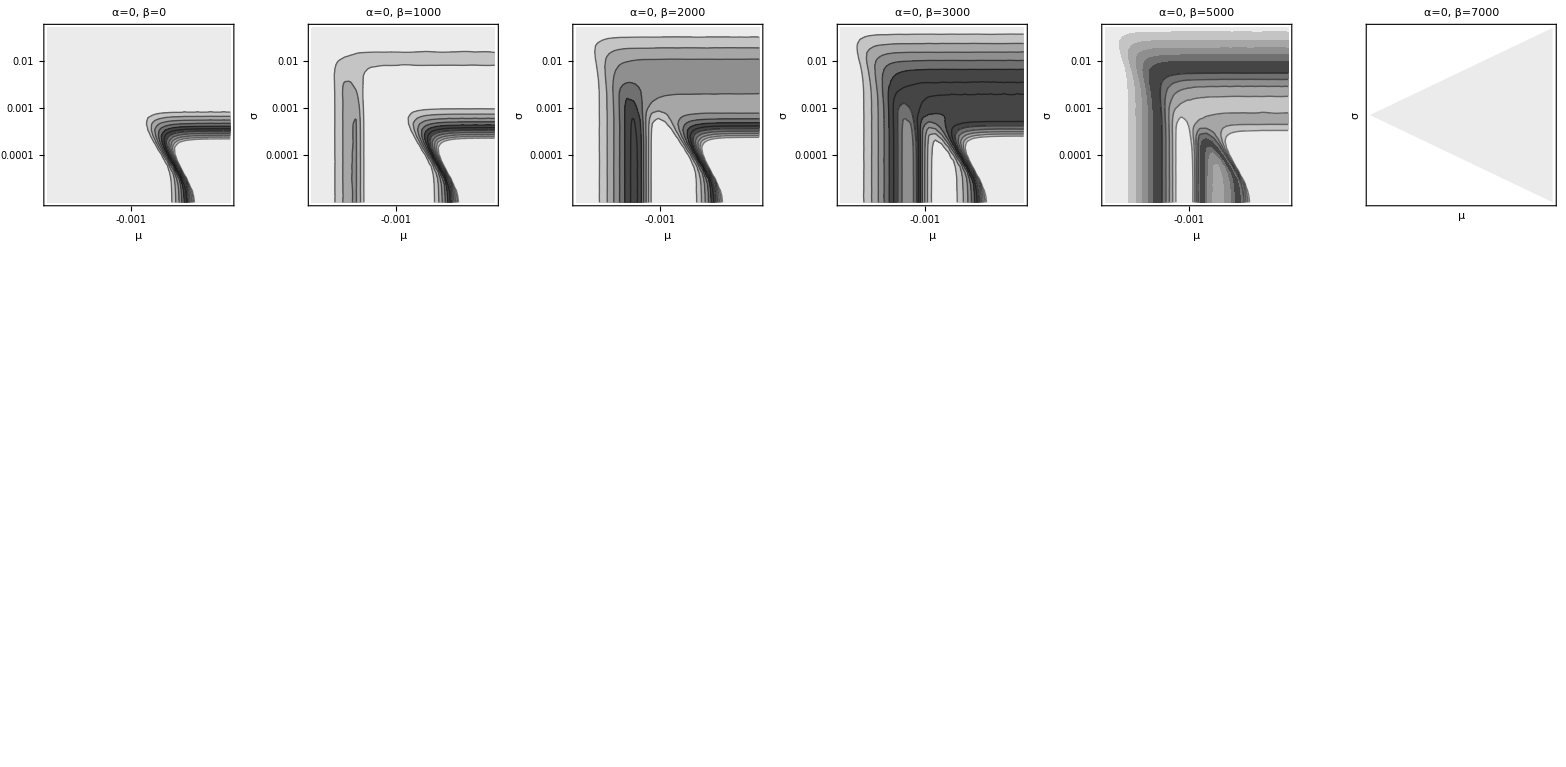

```mathematica
plotsRNS=GraphicsGrid[{{plotRNShetsA0B0,plotRNShetsA0B1000,plotRNShetsA0B2000,plotRNShetsA0B3000,plotRNShetsA0B5000,plotRNShetsA0B7000},{plotRNShetsA2B0,plotRNShetsA2B1000,plotRNShetsA2B2000,plotRNShetsA2B3000,plotRNShetsA2B5000,plotRNShetsA2B7000},{plotRNShetsA4B0,plotRNShetsA4B1000,plotRNShetsA4B2000,plotRNShetsA4B3000,plotRNShetsA4B5000,plotRNShetsA4B7000}},ImageSize->Full]
```

```mathematica
pointsRNSA0B0=Cases[Normal@ContourPlot[RNShetsintA0B0[μ,σ]==0,{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]}],Line[pts_]->pts,Infinity];
```

```mathematica
pointsRNSA0B1000=Cases[Normal@ContourPlot[RNShetsintA0B1000[μ,σ]==0,{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]}],Line[pts_]->pts,Infinity];
```

```mathematica
pointsRNSA0B2000=Cases[Normal@ContourPlot[RNShetsintA0B2000[μ,σ]==0,{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]}],Line[pts_]->pts,Infinity];
```

```mathematica
pointsRNSA0B3000=Cases[Normal@ContourPlot[RNShetsintA0B3000[μ,σ]==0,{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]}],Line[pts_]->pts,Infinity];
```

```mathematica
pointsRNSA0B5000=Cases[Normal@ContourPlot[RNShetsintA0B5000[μ,σ]==0,{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]}],Line[pts_]->pts,Infinity];
```

```mathematica
pointsRNSA0B7000=Cases[Normal@ContourPlot[RNShetsintA0B7000[μ,σ]==0,{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]}],Line[pts_]->pts,Infinity];
```

```mathematica
pointsRNSA2B0=Cases[Normal@ContourPlot[RNShetsintA2B0[μ,σ]==0,{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]}],Line[pts_]->pts,Infinity];
```

```mathematica
pointsRNSA2B1000=Cases[Normal@ContourPlot[RNShetsintA2B1000[μ,σ]==0,{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]}],Line[pts_]->pts,Infinity];
```

```mathematica
pointsRNSA2B2000=Cases[Normal@ContourPlot[RNShetsintA2B2000[μ,σ]==0,{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]}],Line[pts_]->pts,Infinity];
```

```mathematica
pointsRNSA2B3000=Cases[Normal@ContourPlot[RNShetsintA2B3000[μ,σ]==0,{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]}],Line[pts_]->pts,Infinity];
```

```mathematica
pointsRNSA2B5000=Cases[Normal@ContourPlot[RNShetsintA2B5000[μ,σ]==0,{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]}],Line[pts_]->pts,Infinity];
```

```mathematica
pointsRNSA2B7000=Cases[Normal@ContourPlot[RNShetsintA2B7000[μ,σ]==0,{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]}],Line[pts_]->pts,Infinity];
```

```mathematica
pointsRNSA4B0=Cases[Normal@ContourPlot[RNShetsintA4B0[μ,σ]==0,{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]}],Line[pts_]->pts,Infinity];
```

```mathematica
pointsRNSA4B1000=Cases[Normal@ContourPlot[RNShetsintA4B1000[μ,σ]==0,{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]}],Line[pts_]->pts,Infinity];
```

```mathematica
pointsRNSA4B2000=Cases[Normal@ContourPlot[RNShetsintA4B2000[μ,σ]==0,{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]}],Line[pts_]->pts,Infinity];
```

```mathematica
pointsRNSA4B3000=Cases[Normal@ContourPlot[RNShetsintA4B3000[μ,σ]==0,{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]}],Line[pts_]->pts,Infinity];
```

```mathematica
pointsRNSA4B5000=Cases[Normal@ContourPlot[RNShetsintA4B5000[μ,σ]==0,{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]}],Line[pts_]->pts,Infinity];
```

```mathematica
pointsRNSA4B7000=Cases[Normal@ContourPlot[RNShetsintA4B7000[μ,σ]==0,{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]}],Line[pts_]->pts,Infinity];
```

```mathematica
plotsRNSpoints=GraphicsGrid[{{Show[plotRNShetsA0B0,ListPlot[pointsRNSA0B0,PlotStyle->White]],Show[plotRNShetsA0B1000,ListPlot[pointsRNSA0B1000,PlotStyle->White]],Show[plotRNShetsA0B3000,ListPlot[pointsRNSA0B3000,PlotStyle->White]],Show[plotRNShetsA0B5000,ListPlot[pointsRNSA0B5000,PlotStyle->White]],Show[plotRNShetsA0B7000,ListPlot[pointsRNSA0B7000,PlotStyle->White]]},{Show[plotRNShetsA2B0,ListPlot[pointsRNSA2B0,PlotStyle->White]],Show[plotRNShetsA2B1000,ListPlot[pointsRNSA2B1000,PlotStyle->White]],Show[plotRNShetsA2B3000,ListPlot[pointsRNSA2B3000,PlotStyle->White]],Show[plotRNShetsA2B5000,ListPlot[pointsRNSA2B5000,PlotStyle->White]],Show[plotRNShetsA2B7000,ListPlot[pointsRNSA2B7000,PlotStyle->White]]},{Show[plotRNShetsA4B0,ListPlot[pointsRNSA4B0,PlotStyle->White]],Show[plotRNShetsA4B1000,ListPlot[pointsRNSA4B1000,PlotStyle->White]],Show[plotRNShetsA4B3000,ListPlot[pointsRNSA4B3000,PlotStyle->White]],Show[plotRNShetsA4B5000,ListPlot[pointsRNSA4B5000,PlotStyle->White]],Show[plotRNShetsA4B7000,ListPlot[pointsRNSA4B7000,PlotStyle->White]]}},ImageSize->Full]
```

-Graphics-

```mathematica
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/points/hets_points_rns_alpha=0_beta=0.txt",Flatten[pointsRNSA0B0,1]//N];
```

```mathematica
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/points/hets_points_rns_alpha=0_beta=1000.txt",Flatten[pointsRNSA0B1000,1]//N];
```

```mathematica
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/points/hets_points_rns_alpha=0_beta=2000.txt",Flatten[pointsRNSA0B2000,1]//N];
```

```mathematica
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/points/hets_points_rns_alpha=0_beta=3000.txt",Flatten[pointsRNSA0B3000,1]//N];
```

```mathematica
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/points/hets_points_rns_alpha=0_beta=5000.txt",Flatten[pointsRNSA0B5000,1]//N];
```

```mathematica
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/points/hets_points_rns_alpha=0_beta=7000.txt",Flatten[pointsRNSA0B7000,1]//N];
```

```mathematica
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/points/hets_points_rns_alpha=-2_beta=0.txt",Flatten[pointsRNSA2B0,1]//N];
```

```mathematica
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/points/hets_points_rns_alpha=-2_beta=1000.txt",Flatten[pointsRNSA2B1000,1]//N];
```

```mathematica
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/points/hets_points_rns_alpha=-2_beta=2000.txt",Flatten[pointsRNSA2B2000,1]//N];
```

```mathematica
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/points/hets_points_rns_alpha=-2_beta=3000.txt",Flatten[pointsRNSA2B3000,1]//N];
```

```mathematica
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/points/hets_points_rns_alpha=-2_beta=5000.txt",Flatten[pointsRNSA2B5000,1]//N];
```

```mathematica
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/points/hets_points_rns_alpha=-2_beta=7000.txt",Flatten[pointsRNSA2B7000,1]//N];
```

```mathematica
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/points/hets_points_rns_alpha=-4_beta=0.txt",Flatten[pointsRNSA4B0,1]//N];
```

```mathematica
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/points/hets_points_rns_alpha=-4_beta=1000.txt",Flatten[pointsRNSA4B1000,1]//N];
```

```mathematica
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/points/hets_points_rns_alpha=-4_beta=2000.txt",Flatten[pointsRNSA4B2000,1]//N];
```

```mathematica
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/points/hets_points_rns_alpha=-4_beta=3000.txt",Flatten[pointsRNSA4B3000,1]//N];
```

```mathematica
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/points/hets_points_rns_alpha=-4_beta=5000.txt",Flatten[pointsRNSA4B5000,1]//N];
```

```mathematica
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/points/hets_points_rns_alpha=-4_beta=7000.txt",Flatten[pointsRNSA4B7000,1]//N];
```

```mathematica
SBShetsFnormcA0B0={Abs[(#[[5]]-hetsSBS)]/hetsSBS}&/@SBShetsFA0B0;
```

```mathematica
SBShetsFpointsA0B0={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@SBShetsFA0B0;
```

```mathematica
SBSdensFnormcA0B0={Abs[(#[[5]]-densSBS)]/densSBS}&/@SBSdensFA0B0;
```

```mathematica
SBSdensFpointsA0B0={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@SBSdensFA0B0;
```

```mathematica
SBShetsFnormcA0B1000={Abs[(#[[5]]-hetsSBS)]/hetsSBS}&/@SBShetsFA0B1000;
```

```mathematica
SBShetsFpointsA0B1000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@SBShetsFA0B1000;
```

```mathematica
SBSdensFnormcA0B1000={Abs[(#[[5]]-densSBS)]/densSBS}&/@SBSdensFA0B1000;
```

```mathematica
SBSdensFpointsA0B1000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@SBSdensFA0B1000;
```

```mathematica
SBShetsFnormcA0B3000={Abs[(#[[5]]-hetsSBS)]/hetsSBS}&/@SBShetsFA0B3000;
```

```mathematica
SBShetsFpointsA0B3000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@SBShetsFA0B3000;
```

```mathematica
SBSdensFnormcA0B3000={Abs[(#[[5]]-densSBS)]/densSBS}&/@SBSdensFA0B3000;
```

```mathematica
SBSdensFpointsA0B3000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@SBSdensFA0B3000;
```

```mathematica
SBShetsFnormcA0B5000={Abs[(#[[5]]-hetsSBS)]/hetsSBS}&/@SBShetsFA0B5000;
```

```mathematica
SBShetsFpointsA0B5000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@SBShetsFA0B5000;
```

```mathematica
SBSdensFnormcA0B5000={Abs[(#[[5]]-densSBS)]/densSBS}&/@SBSdensFA0B5000;
```

```mathematica
SBSdensFpointsA0B5000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@SBSdensFA0B5000;
```

```mathematica
SBShetsFnormcA0B7000={Abs[(#[[5]]-hetsSBS)]/hetsSBS}&/@SBShetsFA0B7000;
```

```mathematica
SBShetsFpointsA0B7000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@SBShetsFA0B7000;
```

```mathematica
SBSdensFnormcA0B7000={Abs[(#[[5]]-densSBS)]/densSBS}&/@SBSdensFA0B7000;
```

```mathematica
SBSdensFpointsA0B7000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@SBSdensFA0B7000;
```

```mathematica
SBShetsFnormcA2B0={Abs[(#[[5]]-hetsSBS)]/hetsSBS}&/@SBShetsFA2B0;
```

```mathematica
SBShetsFpointsA2B0={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@SBShetsFA2B0;
```

```mathematica
SBSdensFnormcA2B0={Abs[(#[[5]]-densSBS)]/densSBS}&/@SBSdensFA2B0;
```

```mathematica
SBSdensFpointsA2B0={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@SBSdensFA2B0;
```

```mathematica
SBShetsFnormcA2B1000={Abs[(#[[5]]-hetsSBS)]/hetsSBS}&/@SBShetsFA2B1000;
```

```mathematica
SBShetsFpointsA2B1000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@SBShetsFA2B1000;
```

```mathematica
SBSdensFnormcA2B1000={Abs[(#[[5]]-densSBS)]/densSBS}&/@SBSdensFA2B1000;
```

```mathematica
SBSdensFpointsA2B1000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@SBSdensFA2B1000;
```

```mathematica
SBShetsFnormcA2B3000={Abs[(#[[5]]-hetsSBS)]/hetsSBS}&/@SBShetsFA2B3000;
```

```mathematica
SBShetsFpointsA2B3000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@SBShetsFA2B3000;
```

```mathematica
SBSdensFnormcA2B3000={Abs[(#[[5]]-densSBS)]/densSBS}&/@SBSdensFA2B3000;
```

```mathematica
SBSdensFpointsA2B3000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@SBSdensFA2B3000;
```

```mathematica
SBShetsFnormcA2B5000={Abs[(#[[5]]-hetsSBS)]/hetsSBS}&/@SBShetsFA2B5000;
```

```mathematica
SBShetsFpointsA2B5000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@SBShetsFA2B5000;
```

```mathematica
SBSdensFnormcA2B5000={Abs[(#[[5]]-densSBS)]/densSBS}&/@SBSdensFA2B5000;
```

```mathematica
SBSdensFpointsA2B5000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@SBSdensFA2B5000;
```

```mathematica
SBShetsFnormcA2B7000={Abs[(#[[5]]-hetsSBS)]/hetsSBS}&/@SBShetsFA2B7000;
```

```mathematica
SBShetsFpointsA2B7000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@SBShetsFA2B7000;
```

```mathematica
SBSdensFnormcA2B7000={Abs[(#[[5]]-densSBS)]/densSBS}&/@SBSdensFA2B7000;
```

```mathematica
SBSdensFpointsA2B7000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@SBSdensFA2B7000;
```

```mathematica
SBShetsFnormcA4B0={Abs[(#[[5]]-hetsSBS)]/hetsSBS}&/@SBShetsFA4B0;
```

```mathematica
SBShetsFpointsA4B0={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@SBShetsFA4B0;
```

```mathematica
SBSdensFnormcA4B0={Abs[(#[[5]]-densSBS)]/densSBS}&/@SBSdensFA4B0;
```

```mathematica
SBSdensFpointsA4B0={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@SBSdensFA4B0;
```

```mathematica
SBShetsFnormcA4B1000={Abs[(#[[5]]-hetsSBS)]/hetsSBS}&/@SBShetsFA4B1000;
```

```mathematica
SBShetsFpointsA4B1000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@SBShetsFA4B1000;
```

```mathematica
SBSdensFnormcA4B1000={Abs[(#[[5]]-densSBS)]/densSBS}&/@SBSdensFA4B1000;
```

```mathematica
SBSdensFpointsA4B1000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@SBSdensFA4B1000;
```

```mathematica
SBShetsFnormcA4B3000={Abs[(#[[5]]-hetsSBS)]/hetsSBS}&/@SBShetsFA4B3000;
```

```mathematica
SBShetsFpointsA4B3000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@SBShetsFA4B3000;
```

```mathematica
SBSdensFnormcA4B3000={Abs[(#[[5]]-densSBS)]/densSBS}&/@SBSdensFA4B3000;
```

```mathematica
SBSdensFpointsA4B3000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@SBSdensFA4B3000;
```

```mathematica
SBShetsFnormcA4B5000={Abs[(#[[5]]-hetsSBS)]/hetsSBS}&/@SBShetsFA4B5000;
```

```mathematica
SBShetsFpointsA4B5000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@SBShetsFA4B5000;
```

```mathematica
SBSdensFnormcA4B5000={Abs[(#[[5]]-densSBS)]/densSBS}&/@SBSdensFA4B5000;
```

```mathematica
SBSdensFpointsA4B5000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@SBSdensFA4B5000;
```

```mathematica
SBShetsFnormcA4B7000={Abs[(#[[5]]-hetsSBS)]/hetsSBS}&/@SBShetsFA4B7000;
```

```mathematica
SBShetsFpointsA4B7000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@SBShetsFA4B7000;
```

```mathematica
SBSdensFnormcA4B7000={Abs[(#[[5]]-densSBS)]/densSBS}&/@SBSdensFA4B7000;
```

```mathematica
SBSdensFpointsA4B7000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@SBSdensFA4B7000;
```

```mathematica
RNShetsFnormcA0B0={Abs[(#[[5]]-hetsRNS)]/hetsRNS}&/@RNShetsFA0B0;
```

```mathematica
RNShetsFpointsA0B0={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@RNShetsFA0B0;
```

```mathematica
RNSdensFnormcA0B0={Abs[(#[[5]]-densRNS)]/densRNS}&/@RNSdensFA0B0;
```

```mathematica
RNSdensFpointsA0B0={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@RNSdensFA0B0;
```

```mathematica
RNShetsFnormcA0B1000={Abs[(#[[5]]-hetsRNS)]/hetsRNS}&/@RNShetsFA0B1000;
```

```mathematica
RNShetsFpointsA0B1000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@RNShetsFA0B1000;
```

```mathematica
RNSdensFnormcA0B1000={Abs[(#[[5]]-densRNS)]/densRNS}&/@RNSdensFA0B1000;
```

```mathematica
RNSdensFpointsA0B1000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@RNSdensFA0B1000;
```

```mathematica
RNShetsFnormcA0B3000={Abs[(#[[5]]-hetsRNS)]/hetsRNS}&/@RNShetsFA0B3000;
```

```mathematica
RNShetsFpointsA0B3000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@RNShetsFA0B3000;
```

```mathematica
RNSdensFnormcA0B3000={Abs[(#[[5]]-densRNS)]/densRNS}&/@RNSdensFA0B3000;
```

```mathematica
RNSdensFpointsA0B3000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@RNSdensFA0B3000;
```

```mathematica
RNShetsFnormcA0B5000={Abs[(#[[5]]-hetsRNS)]/hetsRNS}&/@RNShetsFA0B5000;
```

```mathematica
RNShetsFpointsA0B5000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@RNShetsFA0B5000;
```

```mathematica
RNSdensFnormcA0B5000={Abs[(#[[5]]-densRNS)]/densRNS}&/@RNSdensFA0B5000;
```

```mathematica
RNSdensFpointsA0B5000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@RNSdensFA0B5000;
```

```mathematica
RNShetsFnormcA0B7000={Abs[(#[[5]]-hetsRNS)]/hetsRNS}&/@RNShetsFA0B7000;
```

```mathematica
RNShetsFpointsA0B7000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@RNShetsFA0B7000;
```

```mathematica
RNSdensFnormcA0B7000={Abs[(#[[5]]-densRNS)]/densRNS}&/@RNSdensFA0B7000;
```

```mathematica
RNSdensFpointsA0B7000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@RNSdensFA0B7000;
```

```mathematica
RNShetsFnormcA2B0={Abs[(#[[5]]-hetsRNS)]/hetsRNS}&/@RNShetsFA2B0;
```

```mathematica
RNShetsFpointsA2B0={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@RNShetsFA2B0;
```

```mathematica
RNSdensFnormcA2B0={Abs[(#[[5]]-densRNS)]/densRNS}&/@RNSdensFA2B0;
```

```mathematica
RNSdensFpointsA2B0={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@RNSdensFA2B0;
```

```mathematica
RNShetsFnormcA2B1000={Abs[(#[[5]]-hetsRNS)]/hetsRNS}&/@RNShetsFA2B1000;
```

```mathematica
RNShetsFpointsA2B1000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@RNShetsFA2B1000;
```

```mathematica
RNSdensFnormcA2B1000={Abs[(#[[5]]-densRNS)]/densRNS}&/@RNSdensFA2B1000;
```

```mathematica
RNSdensFpointsA2B1000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@RNSdensFA2B1000;
```

```mathematica
RNShetsFnormcA2B3000={Abs[(#[[5]]-hetsRNS)]/hetsRNS}&/@RNShetsFA2B3000;
```

```mathematica
RNShetsFpointsA2B3000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@RNShetsFA2B3000;
```

```mathematica
RNSdensFnormcA2B3000={Abs[(#[[5]]-densRNS)]/densRNS}&/@RNSdensFA2B3000;
```

```mathematica
RNSdensFpointsA2B3000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@RNSdensFA2B3000;
```

```mathematica
RNShetsFnormcA2B5000={Abs[(#[[5]]-hetsRNS)]/hetsRNS}&/@RNShetsFA2B5000;
```

```mathematica
RNShetsFpointsA2B5000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@RNShetsFA2B5000;
```

```mathematica
RNSdensFnormcA2B5000={Abs[(#[[5]]-densRNS)]/densRNS}&/@RNSdensFA2B5000;
```

```mathematica
RNSdensFpointsA2B5000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@RNSdensFA2B5000;
```

```mathematica
RNShetsFnormcA2B7000={Abs[(#[[5]]-hetsRNS)]/hetsRNS}&/@RNShetsFA2B7000;
```

```mathematica
RNShetsFpointsA2B7000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@RNShetsFA2B7000;
```

```mathematica
RNSdensFnormcA2B7000={Abs[(#[[5]]-densRNS)]/densRNS}&/@RNSdensFA2B7000;
```

```mathematica
RNSdensFpointsA2B7000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@RNSdensFA2B7000;
```

```mathematica
RNShetsFnormcA4B0={Abs[(#[[5]]-hetsRNS)]/hetsRNS}&/@RNShetsFA4B0;
```

```mathematica
RNShetsFpointsA4B0={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@RNShetsFA4B0;
```

```mathematica
RNSdensFnormcA4B0={Abs[(#[[5]]-densRNS)]/densRNS}&/@RNSdensFA4B0;
```

```mathematica
RNSdensFpointsA4B0={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@RNSdensFA4B0;
```

```mathematica
RNShetsFnormcA4B1000={Abs[(#[[5]]-hetsRNS)]/hetsRNS}&/@RNShetsFA4B1000;
```

```mathematica
RNShetsFpointsA4B1000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@RNShetsFA4B1000;
```

```mathematica
RNSdensFnormcA4B1000={Abs[(#[[5]]-densRNS)]/densRNS}&/@RNSdensFA4B1000;
```

```mathematica
RNSdensFpointsA4B1000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@RNSdensFA4B1000;
```

```mathematica
RNShetsFnormcA4B3000={Abs[(#[[5]]-hetsRNS)]/hetsRNS}&/@RNShetsFA4B3000;
```

```mathematica
RNShetsFpointsA4B3000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@RNShetsFA4B3000;
```

```mathematica
RNSdensFnormcA4B3000={Abs[(#[[5]]-densRNS)]/densRNS}&/@RNSdensFA4B3000;
```

```mathematica
RNSdensFpointsA4B3000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@RNSdensFA4B3000;
```

```mathematica
RNShetsFnormcA4B5000={Abs[(#[[5]]-hetsRNS)]/hetsRNS}&/@RNShetsFA4B5000;
```

```mathematica
RNShetsFpointsA4B5000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@RNShetsFA4B5000;
```

```mathematica
RNSdensFnormcA4B5000={Abs[(#[[5]]-densRNS)]/densRNS}&/@RNSdensFA4B5000;
```

```mathematica
RNSdensFpointsA4B5000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@RNSdensFA4B5000;
```

```mathematica
RNShetsFnormcA4B7000={Abs[(#[[5]]-hetsRNS)]/hetsRNS}&/@RNShetsFA4B7000;
```

```mathematica
RNShetsFpointsA4B7000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@RNShetsFA4B7000;
```

```mathematica
RNSdensFnormcA4B7000={Abs[(#[[5]]-densRNS)]/densRNS}&/@RNSdensFA4B7000;
```

```mathematica
RNSdensFpointsA4B7000={-Log[Abs[#[[1]]]],Log[#[[2]]]}&/@RNSdensFA4B7000;
```

```mathematica
plotRNShetsFA0B0=ListPlot[RNShetsFpointsA0B0,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[RNShetsFnormcA0B0]}[[1]]];
```

```mathematica
plotRNShetsFA0B1000=ListPlot[RNShetsFpointsA0B1000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[RNShetsFnormcA0B1000]}[[1]]];
```

```mathematica
plotRNShetsFA0B3000=ListPlot[RNShetsFpointsA0B3000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[RNShetsFnormcA0B3000]}[[1]]];
```

```mathematica
plotRNShetsFA0B5000=ListPlot[RNShetsFpointsA0B5000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[RNShetsFnormcA0B5000]}[[1]]];
```

```mathematica
plotRNShetsFA0B7000=ListPlot[RNShetsFpointsA0B7000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[RNShetsFnormcA0B7000]}[[1]]];
```

```mathematica
plotRNShetsFA2B0=ListPlot[RNShetsFpointsA2B0,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[RNShetsFnormcA2B0]}[[1]]];
```

```mathematica
plotRNShetsFA2B1000=ListPlot[RNShetsFpointsA2B1000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[RNShetsFnormcA2B1000]}[[1]]];
```

```mathematica
plotRNShetsFA2B3000=ListPlot[RNShetsFpointsA2B3000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[RNShetsFnormcA2B3000]}[[1]]];
```

```mathematica
plotRNShetsFA2B5000=ListPlot[RNShetsFpointsA2B5000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[RNShetsFnormcA2B5000]}[[1]]];
```

```mathematica
plotRNShetsFA2B7000=ListPlot[RNShetsFpointsA2B7000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[RNShetsFnormcA2B7000]}[[1]]];
```

```mathematica
plotRNShetsFA4B0=ListPlot[RNShetsFpointsA4B0,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[RNShetsFnormcA4B0]}[[1]]];
```

```mathematica
plotRNShetsFA4B1000=ListPlot[RNShetsFpointsA4B1000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[RNShetsFnormcA4B1000]}[[1]]];
```

```mathematica
plotRNShetsFA4B3000=ListPlot[RNShetsFpointsA4B3000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[RNShetsFnormcA4B3000]}[[1]]];
```

```mathematica
plotRNShetsFA4B5000=ListPlot[RNShetsFpointsA4B5000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[RNShetsFnormcA4B5000]}[[1]]];
```

```mathematica
plotRNShetsFA4B7000=ListPlot[RNShetsFpointsA4B7000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[RNShetsFnormcA4B7000]}[[1]]];
```

```mathematica
plotSBShetsFA0B0=ListPlot[SBShetsFpointsA0B0,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[SBShetsFnormcA0B0]}[[1]]];
```

```mathematica
plotSBShetsFA0B1000=ListPlot[SBShetsFpointsA0B1000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[SBShetsFnormcA0B1000]}[[1]]];
```

```mathematica
plotSBShetsFA0B3000=ListPlot[SBShetsFpointsA0B3000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[SBShetsFnormcA0B3000]}[[1]]];
```

```mathematica
plotSBShetsFA0B5000=ListPlot[SBShetsFpointsA0B5000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[SBShetsFnormcA0B5000]}[[1]]];
```

```mathematica
plotSBShetsFA0B7000=ListPlot[SBShetsFpointsA0B7000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[SBShetsFnormcA0B7000]}[[1]]];
```

```mathematica
plotSBShetsFA2B0=ListPlot[SBShetsFpointsA2B0,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[SBShetsFnormcA2B0]}[[1]]];
```

```mathematica
plotSBShetsFA2B1000=ListPlot[SBShetsFpointsA2B1000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[SBShetsFnormcA2B1000]}[[1]]];
```

```mathematica
plotSBShetsFA2B3000=ListPlot[SBShetsFpointsA2B3000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[SBShetsFnormcA2B3000]}[[1]]];
```

```mathematica
plotSBShetsFA2B5000=ListPlot[SBShetsFpointsA2B5000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[SBShetsFnormcA2B5000]}[[1]]];
```

```mathematica
plotSBShetsFA2B7000=ListPlot[SBShetsFpointsA2B7000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[SBShetsFnormcA2B7000]}[[1]]];
```

```mathematica
plotSBShetsFA4B0=ListPlot[SBShetsFpointsA4B0,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[SBShetsFnormcA4B0]}[[1]]];
```

```mathematica
plotSBShetsFA4B1000=ListPlot[SBShetsFpointsA4B1000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[SBShetsFnormcA4B1000]}[[1]]];
```

```mathematica
plotSBShetsFA4B3000=ListPlot[SBShetsFpointsA4B3000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[SBShetsFnormcA4B3000]}[[1]]];
```

```mathematica
plotSBShetsFA4B5000=ListPlot[SBShetsFpointsA4B5000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[SBShetsFnormcA4B5000]}[[1]]];
```

```mathematica
plotSBShetsFA4B7000=ListPlot[SBShetsFpointsA4B7000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[SBShetsFnormcA4B7000]}[[1]]];
```

```mathematica
plotRNSdensFA0B0=ListPlot[RNSdensFpointsA0B0,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[RNSdensFnormcA0B0]}[[1]]];
```

```mathematica
plotRNSdensFA0B1000=ListPlot[RNSdensFpointsA0B1000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[RNSdensFnormcA0B1000]}[[1]]];
```

```mathematica
plotRNSdensFA0B3000=ListPlot[RNSdensFpointsA0B3000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[RNSdensFnormcA0B3000]}[[1]]];
```

```mathematica
plotRNSdensFA0B5000=ListPlot[RNSdensFpointsA0B5000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[RNSdensFnormcA0B5000]}[[1]]];
```

```mathematica
plotRNSdensFA0B7000=ListPlot[RNSdensFpointsA0B7000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[RNSdensFnormcA0B7000]}[[1]]];
```

```mathematica
plotRNSdensFA2B0=ListPlot[RNSdensFpointsA2B0,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[RNSdensFnormcA2B0]}[[1]]];
```

```mathematica
plotRNSdensFA2B1000=ListPlot[RNSdensFpointsA2B1000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[RNSdensFnormcA2B1000]}[[1]]];
```

```mathematica
plotRNSdensFA2B3000=ListPlot[RNSdensFpointsA2B3000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[RNSdensFnormcA2B3000]}[[1]]];
```

```mathematica
plotRNSdensFA2B5000=ListPlot[RNSdensFpointsA2B5000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[RNSdensFnormcA2B5000]}[[1]]];
```

```mathematica
plotRNSdensFA2B7000=ListPlot[RNSdensFpointsA2B7000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[RNSdensFnormcA2B7000]}[[1]]];
```

```mathematica
plotRNSdensFA4B0=ListPlot[RNSdensFpointsA4B0,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[RNSdensFnormcA4B0]}[[1]]];
```

```mathematica
plotRNSdensFA4B1000=ListPlot[RNSdensFpointsA4B1000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[RNSdensFnormcA4B1000]}[[1]]];
```

```mathematica
plotRNSdensFA4B3000=ListPlot[RNSdensFpointsA4B3000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[RNSdensFnormcA4B3000]}[[1]]];
```

```mathematica
plotRNSdensFA4B5000=ListPlot[RNSdensFpointsA4B5000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[RNSdensFnormcA4B5000]}[[1]]];
```

```mathematica
plotRNSdensFA4B7000=ListPlot[RNSdensFpointsA4B7000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[RNSdensFnormcA4B7000]}[[1]]];
```

```mathematica
plotSBSdensFA0B0=ListPlot[SBSdensFpointsA0B0,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[SBSdensFnormcA0B0]}[[1]]];
```

```mathematica
plotSBSdensFA0B1000=ListPlot[SBSdensFpointsA0B1000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[SBSdensFnormcA0B1000]}[[1]]];
```

```mathematica
plotSBSdensFA0B3000=ListPlot[SBSdensFpointsA0B3000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[SBSdensFnormcA0B3000]}[[1]]];
```

```mathematica
plotSBSdensFA0B5000=ListPlot[SBSdensFpointsA0B5000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[SBSdensFnormcA0B5000]}[[1]]];
```

```mathematica
plotSBSdensFA0B7000=ListPlot[SBSdensFpointsA0B7000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[SBSdensFnormcA0B7000]}[[1]]];
```

```mathematica
plotSBSdensFA2B0=ListPlot[SBSdensFpointsA2B0,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[SBSdensFnormcA2B0]}[[1]]];
```

```mathematica
plotSBSdensFA2B1000=ListPlot[SBSdensFpointsA2B1000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[SBSdensFnormcA2B1000]}[[1]]];
```

```mathematica
plotSBSdensFA2B3000=ListPlot[SBSdensFpointsA2B3000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[SBSdensFnormcA2B3000]}[[1]]];
```

```mathematica
plotSBSdensFA2B5000=ListPlot[SBSdensFpointsA2B5000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[SBSdensFnormcA2B5000]}[[1]]];
```

```mathematica
plotSBSdensFA2B7000=ListPlot[SBSdensFpointsA2B7000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[SBSdensFnormcA2B7000]}[[1]]];
```

```mathematica
plotSBSdensFA4B0=ListPlot[SBSdensFpointsA4B0,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[SBSdensFnormcA4B0]}[[1]]];
```

```mathematica
plotSBSdensFA4B1000=ListPlot[SBSdensFpointsA4B1000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[SBSdensFnormcA4B1000]}[[1]]];
```

```mathematica
plotSBSdensFA4B3000=ListPlot[SBSdensFpointsA4B3000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[SBSdensFnormcA4B3000]}[[1]]];
```

```mathematica
plotSBSdensFA4B5000=ListPlot[SBSdensFpointsA4B5000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[SBSdensFnormcA4B5000]}[[1]]];
```

```mathematica
plotSBSdensFA4B7000=ListPlot[SBSdensFpointsA4B7000,PlotStyle->PointSize[0.01]]/.Point[args_]:>Point[args,VertexColors->{bothc[#]&/@Flatten[SBSdensFnormcA4B7000]}[[1]]];
```

```mathematica
area[-0.0001,0.0001,0]
```

0.

```mathematica
Show[plotRNShetsA0B3000,plotRNShetsFA0B3000,int0plot]
```

-Graphics-

```mathematica
plotsRNSpointsRNShetsF=
Labeled[GraphicsGrid[{{Show[plotRNShetsA0B0,plotRNShetsFA0B0],Show[plotRNShetsA0B1000,plotRNShetsFA0B1000],Show[plotRNShetsA0B3000,plotRNShetsFA0B3000],Show[plotRNShetsA0B5000,plotRNShetsFA0B5000],Show[plotRNShetsA0B7000,plotRNShetsFA0B7000]},{Show[plotRNShetsA2B0,plotRNShetsFA2B0],Show[plotRNShetsA2B1000,plotRNShetsFA2B1000],Show[plotRNShetsA2B3000,plotRNShetsFA2B3000],Show[plotRNShetsA2B5000,plotRNShetsFA2B5000],Show[plotRNShetsA2B7000,plotRNShetsFA2B7000]},{Show[plotRNShetsA4B0,plotRNShetsFA4B0],Show[plotRNShetsA4B1000,plotRNShetsFA4B1000],Show[plotRNShetsA4B3000,plotRNShetsFA4B3000],Show[plotRNShetsA4B5000,plotRNShetsFA4B5000],Show[plotRNShetsA4B7000,plotRNShetsFA4B7000]}},ImageSize->Full],{"relative error in rns het in orange\n"},{Top},RotateLabel->True,LabelStyle->Directive[FontFamily->"Helvetica",FontSize->18]
];
```

```mathematica
plotsRNSpointsRNShetsFint=
Labeled[GraphicsGrid[{{Show[plotRNShetsA0B0,plotRNShetsFA0B0,int0plot],Show[plotRNShetsA0B1000,plotRNShetsFA0B1000,int0plot],Show[plotRNShetsA0B3000,plotRNShetsFA0B3000,int0plot],Show[plotRNShetsA0B5000,plotRNShetsFA0B5000,int0plot],Show[plotRNShetsA0B7000,plotRNShetsFA0B7000,int0plot]},{Show[plotRNShetsA2B0,plotRNShetsFA2B0,int2plot],Show[plotRNShetsA2B1000,plotRNShetsFA2B1000,int2plot],Show[plotRNShetsA2B3000,plotRNShetsFA2B3000,int2plot],Show[plotRNShetsA2B5000,plotRNShetsFA2B5000,int2plot],Show[plotRNShetsA2B7000,plotRNShetsFA2B7000,int2plot]},{Show[plotRNShetsA4B0,plotRNShetsFA4B0,int4plot],Show[plotRNShetsA4B1000,plotRNShetsFA4B1000,int4plot],Show[plotRNShetsA4B3000,plotRNShetsFA4B3000,int4plot],Show[plotRNShetsA4B5000,plotRNShetsFA4B5000,int4plot],Show[plotRNShetsA4B7000,plotRNShetsFA4B7000,int4plot]}},ImageSize->Full],{"relative error in rns het in orange\n"},{Top},RotateLabel->True,LabelStyle->Directive[FontFamily->"Helvetica",FontSize->18]
]
```

-Graphics-relative error in rns het in orange

```mathematica
plotsRNSpointsRNSdensF=Labeled[GraphicsGrid[{{Show[plotRNShetsA0B0,plotRNSdensFA0B0],Show[plotRNShetsA0B1000,plotRNSdensFA0B1000],Show[plotRNShetsA0B3000,plotRNSdensFA0B3000],Show[plotRNShetsA0B5000,plotRNSdensFA0B5000],Show[plotRNShetsA0B7000,plotRNSdensFA0B7000]},{Show[plotRNShetsA2B0,plotRNSdensFA2B0],Show[plotRNShetsA2B1000,plotRNSdensFA2B1000],Show[plotRNShetsA2B3000,plotRNSdensFA2B3000],Show[plotRNShetsA2B5000,plotRNSdensFA2B5000],Show[plotRNShetsA2B7000,plotRNSdensFA2B7000]},{Show[plotRNShetsA4B0,plotRNSdensFA4B0],Show[plotRNShetsA4B1000,plotRNSdensFA4B1000],Show[plotRNShetsA4B3000,plotRNSdensFA4B3000],Show[plotRNShetsA4B5000,plotRNSdensFA4B5000],Show[plotRNShetsA4B7000,plotRNSdensFA4B7000]}},ImageSize->Full],{"relative error in rns pols in orange\n"},{Top},RotateLabel->True,LabelStyle->Directive[FontFamily->"Helvetica",FontSize->18]
];
```

```mathematica
plotsRNSpointsRNSdensFint=Labeled[GraphicsGrid[{{Show[plotRNShetsA0B0,plotRNSdensFA0B0,int0plot],Show[plotRNShetsA0B1000,plotRNSdensFA0B1000,int0plot],Show[plotRNShetsA0B3000,plotRNSdensFA0B3000,int0plot],Show[plotRNShetsA0B5000,plotRNSdensFA0B5000,int0plot],Show[plotRNShetsA0B7000,plotRNSdensFA0B7000,int0plot]},{Show[plotRNShetsA2B0,plotRNSdensFA2B0,int2plot],Show[plotRNShetsA2B1000,plotRNSdensFA2B1000,int2plot],Show[plotRNShetsA2B3000,plotRNSdensFA2B3000,int2plot],Show[plotRNShetsA2B5000,plotRNSdensFA2B5000,int2plot],Show[plotRNShetsA2B7000,plotRNSdensFA2B7000,int2plot]},{Show[plotRNShetsA4B0,plotRNSdensFA4B0,int4plot],Show[plotRNShetsA4B1000,plotRNSdensFA4B1000,int4plot],Show[plotRNShetsA4B3000,plotRNSdensFA4B3000,int4plot],Show[plotRNShetsA4B5000,plotRNSdensFA4B5000,int4plot],Show[plotRNShetsA4B7000,plotRNSdensFA4B7000,int4plot]}},ImageSize->Full],{"relative error in rns pols in orange\n"},{Top},RotateLabel->True,LabelStyle->Directive[FontFamily->"Helvetica",FontSize->18]
]
```

-Graphics-relative error in rns pols in orange

```mathematica
plotsRNSpointsSBShetsF=Labeled[GraphicsGrid[{{Show[plotRNShetsA0B0,plotSBShetsFA0B0],Show[plotRNShetsA0B1000,plotSBShetsFA0B1000],Show[plotRNShetsA0B3000,plotSBShetsFA0B3000],Show[plotRNShetsA0B5000,plotSBShetsFA0B5000],Show[plotRNShetsA0B7000,plotSBShetsFA0B7000]},{Show[plotRNShetsA2B0,plotSBShetsFA2B0],Show[plotRNShetsA2B1000,plotSBShetsFA2B1000],Show[plotRNShetsA2B3000,plotSBShetsFA2B3000],Show[plotRNShetsA2B5000,plotSBShetsFA2B5000],Show[plotRNShetsA2B7000,plotSBShetsFA2B7000]},{Show[plotRNShetsA4B0,plotSBShetsFA4B0],Show[plotRNShetsA4B1000,plotSBShetsFA4B1000],Show[plotRNShetsA4B3000,plotSBShetsFA4B3000],Show[plotRNShetsA4B5000,plotSBShetsFA4B5000],Show[plotRNShetsA4B7000,plotSBShetsFA4B7000]}},ImageSize->Full],{"relative error in sbs het in orange\n"},{Top},RotateLabel->True,LabelStyle->Directive[FontFamily->"Helvetica",FontSize->18]
];
```

```mathematica
plotsRNSpointsSBShetsFint=Labeled[GraphicsGrid[{{Show[plotRNShetsA0B0,plotSBShetsFA0B0,int0plot],Show[plotRNShetsA0B1000,plotSBShetsFA0B1000,int0plot],Show[plotRNShetsA0B3000,plotSBShetsFA0B3000,int0plot],Show[plotRNShetsA0B5000,plotSBShetsFA0B5000,int0plot],Show[plotRNShetsA0B7000,plotSBShetsFA0B7000,int0plot]},{Show[plotRNShetsA2B0,plotSBShetsFA2B0,int2plot],Show[plotRNShetsA2B1000,plotSBShetsFA2B1000,int2plot],Show[plotRNShetsA2B3000,plotSBShetsFA2B3000,int2plot],Show[plotRNShetsA2B5000,plotSBShetsFA2B5000,int2plot],Show[plotRNShetsA2B7000,plotSBShetsFA2B7000,int2plot]},{Show[plotRNShetsA4B0,plotSBShetsFA4B0,int4plot],Show[plotRNShetsA4B1000,plotSBShetsFA4B1000,int4plot],Show[plotRNShetsA4B3000,plotSBShetsFA4B3000,int4plot],Show[plotRNShetsA4B5000,plotSBShetsFA4B5000,int4plot],Show[plotRNShetsA4B7000,plotSBShetsFA4B7000,int4plot]}},ImageSize->Full],{"relative error in sbs het in orange\n"},{Top},RotateLabel->True,LabelStyle->Directive[FontFamily->"Helvetica",FontSize->18]
]
```

-Graphics-relative error in sbs het in orange

```mathematica
plotsRNSpointsSBSdensF=Labeled[GraphicsGrid[{{Show[plotRNShetsA0B0,plotSBSdensFA0B0],Show[plotRNShetsA0B1000,plotSBSdensFA0B1000],Show[plotRNShetsA0B3000,plotSBSdensFA0B3000],Show[plotRNShetsA0B5000,plotSBSdensFA0B5000],Show[plotRNShetsA0B7000,plotSBSdensFA0B7000]},{Show[plotRNShetsA2B0,plotSBSdensFA2B0],Show[plotRNShetsA2B1000,plotSBSdensFA2B1000],Show[plotRNShetsA2B3000,plotSBSdensFA2B3000],Show[plotRNShetsA2B5000,plotSBSdensFA2B5000],Show[plotRNShetsA2B7000,plotSBSdensFA2B7000]},{Show[plotRNShetsA4B0,plotSBSdensFA4B0],Show[plotRNShetsA4B1000,plotSBSdensFA4B1000],Show[plotRNShetsA4B3000,plotSBSdensFA4B3000],Show[plotRNShetsA4B5000,plotSBSdensFA4B5000],Show[plotRNShetsA4B7000,plotSBSdensFA4B7000]}},ImageSize->Full],{"relative error in sbs pols in orange\n"},{Top},RotateLabel->True,LabelStyle->Directive[FontFamily->"Helvetica",FontSize->18]
];
```

```mathematica
plotsRNSpointsSBSdensFint=Labeled[GraphicsGrid[{{Show[plotRNShetsA0B0,plotSBSdensFA0B0,int0plot],Show[plotRNShetsA0B1000,plotSBSdensFA0B1000,int0plot],Show[plotRNShetsA0B3000,plotSBSdensFA0B3000,int0plot],Show[plotRNShetsA0B5000,plotSBSdensFA0B5000,int0plot],Show[plotRNShetsA0B7000,plotSBSdensFA0B7000,int0plot]},{Show[plotRNShetsA2B0,plotSBSdensFA2B0,int2plot],Show[plotRNShetsA2B1000,plotSBSdensFA2B1000,int2plot],Show[plotRNShetsA2B3000,plotSBSdensFA2B3000,int2plot],Show[plotRNShetsA2B5000,plotSBSdensFA2B5000,int2plot],Show[plotRNShetsA2B7000,plotSBSdensFA2B7000,int2plot]},{Show[plotRNShetsA4B0,plotSBSdensFA4B0,int2plot],Show[plotRNShetsA4B1000,plotSBSdensFA4B1000,int2plot],Show[plotRNShetsA4B3000,plotSBSdensFA4B3000,int2plot],Show[plotRNShetsA4B5000,plotSBSdensFA4B5000,int2plot],Show[plotRNShetsA4B7000,plotSBSdensFA4B7000,int2plot]}},ImageSize->Full],{"relative error in sbs pols in orange\n"},{Top},RotateLabel->True,LabelStyle->Directive[FontFamily->"Helvetica",FontSize->18]
]
```

-Graphics-relative error in sbs pols in orange